```mathematica
(*DEFINE PARAMETERS*)
```

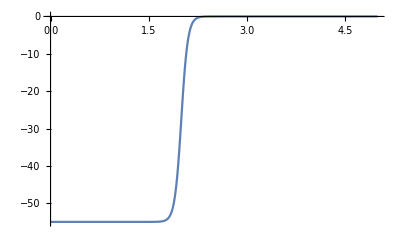

```mathematica
Subscript[m, N]=940;ℏc=197.327;
V0=55;R=2;a=0.05;μ=8/9 Subscript[m, N];
rmax=5.;dr=0.01;
rlist=Range[0,rmax,dr];
len=Length[rlist];
V[r_]:=-V0/(1+Exp[(r-R)/a]);
Vmat=DiagonalMatrix[V[rlist]];
ListLinePlot[V[rlist],DataRange->{0,rmax}]
```

```mathematica
(*DEFINE REQUIRED FUNCTIONS*)
one[n_,d_]:=
DiagonalMatrix[1+0Range[n-Abs[d]],d];
H0=Vmat+-ℏc^2/(2 μ) 1/dr^2(one[len,-1]-2 one[len,0]+one[len,1]);
k[En_?NumericQ]:=Sqrt[(2μ En)/ℏc^2];
B[En_?NumericQ,δ_?NumericQ]:=rmax Cot[k[En] rmax+δ] k[En];
Hnew[En_?NumericQ,δ_?NumericQ]:=(H=H0;H[[len,len]]=Vmat[[len,len]]+-ℏc^2/(2 μ) 1/dr^2(dr B[En,δ]/rmax-1);H)
eigenv[En_?NumericQ,n_,δ_?NumericQ]:=({eval,evec}=Transpose@SortBy[Transpose[Eigensystem[Hnew[En,δ]]],First];eval[[n]]);
findnd[En_]:=Module[{n=1},While[Max[Table[eigenv[En,n,δ],{δ,0.,π,0.1}]]<En,n++;];δ=x/.FindRoot[eigenv[En,n,x]==En,{x,0.,-Pi,Pi}];If[δ<0,δ=π+δ];{n,δ}];
(*eigenv[{En_?NumericQ,i_?NumericQ,δ_?NumericQ}]:=({eval,evec}=Transpose@SortBy[Transpose[Eigensystem[Hnew[En,δ]]],First];{eval[[i]],δ});*)
(*findnd[En_]:=Module[{phase=List[],n=1},(While[Max[Table[eigenv[{En,n,δ}][[1]],{δ,0.,π,0.1}]]<En,n++;];phase=Table[{eigenv[{En,n,δ}][[1]],δ},{δ,0,π,0.01}];δ=phase[[Position[phase[[All,1]],Nearest[phase[[All,1]],En][[1]]][[1,1]],2]];{n,δ})]*)
wave[En_,r_,δ_]:=1/r Sin[k[En] r+δ];
const[i_]:=evec[[i,-1]]/wave[eval[[i]],rmax,δ];
wvplot[En_]:=Module[{n=findnd[En][[1]],δ=findnd[En][[2]]},{eval,evec}=Transpose@SortBy[Transpose[Eigensystem[Hnew[En,δ]]],First];Print[{En,eval[[n]],n,δ}];ListLinePlot[{Transpose[{rlist,evec⟦n⟧}],Transpose[{Range[rmax,rmaxx,dr],const[n] wave[eval[[n]],Range[rmax,rmaxx,dr],δ]}]},PlotRange->All]]
```

{25,25.,3,1.42997}

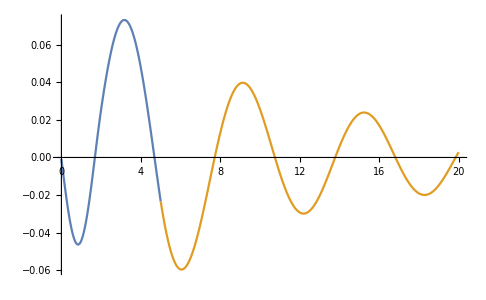
{16.332,-Graphics-}

```mathematica
(*PLOT with {ENERGY, EIGENVALUE, n, PHASE}*)
rmaxx=20.;
wvplot[25]//Timing
```

```mathematica
DiscretePlot[findnd[x][[2]],{x,10,100,1}]
```

$Aborted